```mathematica
With[{xAct`xTensor`Private`xTensorSymbols=DeleteCases[Join[Names["xAct`xTensor`*"],Names["xAct`xTensor`Private`*"]],"$Version"|"xAct`xTensor`$Version"|"$xPermVersionExpected"|"xAct`xTensor`$xPermVersionExpected"|"xAct`xTensor`$ReadingVerbose"]},
Unprotect/@xAct`xTensor`Private`xTensorSymbols;
Clear/@xAct`xTensor`Private`xTensorSymbols;
]
<<xAct`xTensor`;
<<xAct`xCoba`;
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

# Define metric

## General metric in λ, χ ... section

```mathematica
Gsec[ρ_,ϕ_,coordNames_,μ_,ν_]:=Module[{L,M,a,Da},
(*Calculate the geometric tensor for parameters of the Hartree-Bose method.
- HB model magnitudes Subscript[ρ, i], complex phases Subscript[ϕ, i],
   - For D bosons, there will be D-1 parameters due to normalization,
   - coordNames hold the names of state maniifold coordinate map. It is necessary to write down because of symbolic derivatives, 
   - μ, ν are indices of manifold 
*)
L=Length[ρ];

M=√(1+ρ.ρ);
a=Flatten@{1/M,ρ Exp[I ϕ]/M};
Da[m_]:=-1/M^3 ρ.D[ρ,coordNames[[m]]];
(*Da[μ]=D[a[[0]],μ]a0+Conjugate@Sum[D[a[[l]],μ],{l,1,K}]a[[l]];*)
Da[1]

]
Gsec[{1,2,4 λ},{2,2,3},{λ,χ},1,1]
```

-(16 λ)/((6+16 λ^2)^(3/2))

## Metric for class of groundstates

```mathematica
gf[K_]:=Module[{ρA,ϕA,m,gρρ,gϕϕ,zeros},
(*ρA=Indexed[ρ,#]&/@Range[K];*)
ρA=ToExpression["ρ"<>ToString[#]]&/@Range[K-1];
m=1+ρA.ρA;
gρρ=N Table[1/m^2(KroneckerDelta[i,j]m-ρA[[i]]ρA[[j]]),{i,1,K-1},{j,1,K-1}];
gϕϕ=N Table[1/m^2(KroneckerDelta[i,j]m ρA[[i]]^2-ρA[[i]]^2 ρA[[j]]^2),{i,1,K-1},{j,1,K-1}];
zeros=ConstantArray[0,{K-1,K-1}];
ArrayReshape[{Transpose@{gρρ,zeros},Transpose@{zeros,gϕϕ}},{2K-2,2K-2}]/.Flatten[{ρA[[#]]->ρA[[#]][]}&/@Range[K-1]]//FullSimplify
]
gf[3]//MatrixForm
```

((N (1+ρ2[]^2))/((1+ρ1[]^2+ρ2[]^2)^2) | -(N ρ1[] ρ2[])/((1+ρ1[]^2+ρ2[]^2)^2) | 0 | 0
-(N ρ1[] ρ2[])/((1+ρ1[]^2+ρ2[]^2)^2) | (N (1+ρ1[]^2))/((1+ρ1[]^2+ρ2[]^2)^2) | 0 | 0
0 | 0 | (N ρ1[]^2 (1+ρ2[]^2))/((1+ρ1[]^2+ρ2[]^2)^2) | -(N ρ1[]^2 ρ2[]^2)/((1+ρ1[]^2+ρ2[]^2)^2)
0 | 0 | -(N ρ1[]^2 ρ2[]^2)/((1+ρ1[]^2+ρ2[]^2)^2) | (N (1+ρ1[]^2) ρ2[]^2)/((1+ρ1[]^2+ρ2[]^2)^2))

## Coordinate change

```mathematica
Integrate[1/(1+ρ^2),ρ]
```

ArcTan[ρ]

```mathematica
2
```

2

```mathematica
ρ/(1+ρ^2)1/(κ Sin[1/κ ArcTan[ρ]])//FullSimplify
```

(ρ Csc[ArcTan[ρ]/κ])/(κ+κ ρ^2)

```mathematica
Integrate[1/Sin[θ],θ]
```

-Log[Cos[θ/2]]+Log[Sin[θ/2]]

```mathematica
Solve[ρ/(1+ρ^2)==κ Sin[θ],ρ]
```

{{ρ→-(Csc[θ] (-1-√(1-4 κ^2 Sin[θ]^2)))/(2 κ)},{ρ→-(Csc[θ] (-1+√(1-4 κ^2 Sin[θ]^2)))/(2 κ)}}

```mathematica
FullSimplify[D[(1+√(1-4 κ^2 Sin[θ]^2))/(2 κ Sin[θ]),θ],Assumptions->{π>θ>0,κ>0}]
```

-(Cot[θ] Csc[θ]+(Cot[θ] Csc[θ])/(√(1-4 κ^2 Sin[θ]^2)))/(2 κ)

```mathematica
FullSimplify[D[(1-√(1-4 κ^2 Sin[θ]^2))/(2 κ Sin[θ]),θ],Assumptions->{π>θ>0,κ>0}]
```

(Cot[θ] Csc[θ] (-1+1/(√(1-4 κ^2 Sin[θ]^2))))/(2 κ)

```mathematica
Solve[1/(1+((1+√(1-4 κ^2 Sin[θ]^2))/(2 κ Sin[θ]))^2)(-(Cot[θ] Csc[θ]+(Cot[θ] Csc[θ])/(√(1-4 κ^2 Sin[θ]^2)))/(2 κ))==κ^2,θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→ArcCot[(-(κ √(-1+κ^2) √(-((-1-(2 κ √(-1+κ^2))/(√(-1+4 κ^4))) (1-(2 κ √(-1+κ^2))/(√(-1+4 κ^4))))))/(√(-1+4 κ^4))+(4 κ^5 √(-1+κ^2) √(-((-1-(2 κ √(-1+κ^2))/(√(-1+4 κ^4))) (1-(2 κ √(-1+κ^2))/(√(-1+4 κ^4))))))/(√(-1+4 κ^4)))/(-1+κ^2)]},{θ→ArcCot[((κ √(-1+κ^2) √(-((-1+(2 κ √(-1+κ^2))/(√(-1+4 κ^4))) (1+(2 κ √(-1+κ^2))/(√(-1+4 κ^4))))))/(√(-1+4 κ^4))-(4 κ^5 √(-1+κ^2) √(-((-1+(2 κ √(-1+κ^2))/(√(-1+4 κ^4))) (1+(2 κ √(-1+κ^2))/(√(-1+4 κ^4))))))/(√(-1+4 κ^4)))/(-1+κ^2)]}}

```mathematica
solth=Solve[Sin[θ]==ρ/(N r(1+ρ^2)),ρ]
```

{{ρ→(Csc[θ] (1+√(1-4 N^2 r^2 Sin[θ]^2)))/(2 N r)},{ρ→(Csc[θ]-Csc[θ] √(1-4 N^2 r^2 Sin[θ]^2))/(2 N r)}}

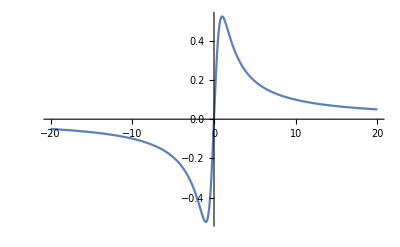

```mathematica
Plot[ArcSin[ρ/(1+ρ^2)],{ρ,-20,20}]
```

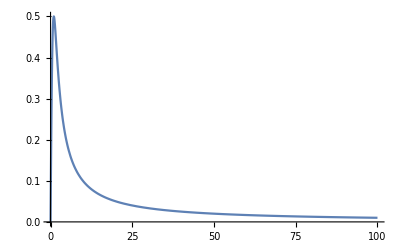

```mathematica
Plot[r/(1+r^2),{r,0,100},PlotRange->All]
```

```mathematica
FullSimplify[D[ArcSin[ρ/(κ(1+ρ^2))],ρ],Assumptions->{r>0,κ>0}]
```

(1-ρ^2)/(κ (1+ρ^2)^2 √(1-ρ^2/(κ^2 (1+ρ^2)^2)))

```mathematica
Solve[1/(1+ρ^2)==Abs[1-ρ^2]/((1+ρ^2)^2 √(1-ρ^2/(κ^2 (1+ρ^2)^2))),ρ,Assumptions->{κ>0}]
```

{{ρ→0}}

```mathematica
Solve[ (1+ρ^2)^2(1-ρ^2/(κ^2 (1+ρ^2)^2))==(1-ρ^2)^2,ρ]
```

{{ρ→0},{ρ→0}}

```mathematica
FullSimplify[Solve[1/κ^2(1+A)^2(1-A/(κ^2(1+A)))==1-2A+A^2,A],Assumptions->{n>0,κ>0,r>0}]
```

{{A→-(1-2 (κ^2+κ^4)+√(1-8 κ^4+16 κ^6))/(2 (1-κ^2+κ^4))},{A→(-1+2 (κ^2+κ^4)+√(1-8 κ^4+16 κ^6))/(2 (1-κ^2+κ^4))}}

# test for Schwarzschild metric

```mathematica
ρAA={ρ1,ρ2,ϕ1,ϕ2};
```

```mathematica
gS=DiagonalMatrix[{-(1-rs/r)c^2,(1-rs/r)^-1,r^2,r^2 Sin[θ]^2}]/.{t->ρ1,r->ρ2,θ->ϕ1,ϕ->ϕ2}/.Flatten[{ρAA[[#]]->ρAA[[#]][]}&/@Range[4]]
```

{{c^2 (-1+rs/ρ2[]),0,0,0},{0,1/(1-rs/ρ2[]),0,0},{0,0,ρ2[]^2,0},{0,0,0,Sin[ϕ1[]]^2 ρ2[]^2}}

```mathematica
(*Define the manifold*)
DefManifold[Ms,4,{a,b,c,d}]
```

** DefManifold: Defining manifold Ms.

** DefVBundle: Defining vbundle TangentMs.

```mathematica
(*Define coordinates on a chart of M*)
DefChart[chs,Ms,{0,1,2,3},{ρ1[],ρ2[],ϕ1[],ϕ2[]},ChartColor->Blue]
```

** DefChart: Defining chart chs.

** DefTensor: Defining coordinate scalar ρ1[].

** DefTensor: Defining coordinate scalar ρ2[].

** DefTensor: Defining coordinate scalar ϕ1[].

** DefTensor: Defining coordinate scalar ϕ2[].

** DefMapping: Defining mapping chs.

** DefMapping: Defining inverse mapping ichs.

** DefTensor: Defining mapping differential tensor dichs[-a,ichsa].

** DefTensor: Defining mapping differential tensor dchs[-a,chsa].

** DefBasis: Defining basis chs. Coordinated basis.

** DefCovD: Defining parallel derivative PDchs[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDchs[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDchs[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDchs[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDchs[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpchs[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownchs[-a,-b,-c,-d].

```mathematica
(*Create the metric tensor in terms of its coordinate components*)
mets=CTensor[gS,{-chs,-chs}]
```

CTensor[{{c^2 (-1+rs/ρ2),0,0,0},{0,1/(1-rs/ρ2),0,0},{0,0,ρ2^2,0},{0,0,0,Sin[ϕ1]^2 ρ2^2}},{-chs,-chs},0]

```mathematica
(*Set this metric to be the metric of the manifold on the chart ch*)
SetCMetric[mets,chs,SignatureOfMetric->{3,1,0}]
```

```mathematica
(*Define the covariant derivative operator*)
cd=CovDOfMetric[mets];
```

```mathematica
(*Calculate various curvature tensors and cache*)
MetricCompute[mets,chs,All]
```

## Show the results

```mathematica
Riemann[cd][-a,-b,-c,-d]/.rs->2G M/c^2
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(2 G M)/ρ2^3 | 0 | 0
(2 G M)/ρ2^3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(G M ((2 G M)/c^2-ρ2))/ρ2^2 | 0
0 | 0 | 0 | 0
(G M ((2 G M)/c^2-ρ2))/ρ2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(G M Sin[ϕ1]^2 ((2 G M)/c^2-ρ2))/ρ2^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(G M Sin[ϕ1]^2 ((2 G M)/c^2-ρ2))/ρ2^2 | 0 | 0 | 0
0 | (2 G M)/ρ2^3 | 0 | 0
-(2 G M)/ρ2^3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (2 G M)/(c^2 ((4 G M)/c^2-2 ρ2)) | 0
0 | -(2 G M)/(c^2 ((4 G M)/c^2-2 ρ2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (2 G M Sin[ϕ1]^2)/(c^2 ((4 G M)/c^2-2 ρ2))
0 | 0 | 0 | 0
0 | -(2 G M Sin[ϕ1]^2)/(c^2 ((4 G M)/c^2-2 ρ2)) | 0 | 0
0 | 0 | (G M ((2 G M)/c^2-ρ2))/ρ2^2 | 0
0 | 0 | 0 | 0
-(G M ((2 G M)/c^2-ρ2))/ρ2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(2 G M)/(c^2 ((4 G M)/c^2-2 ρ2)) | 0
0 | (2 G M)/(c^2 ((4 G M)/c^2-2 ρ2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (2 G M Sin[ϕ1]^2 ρ2)/c^2
0 | 0 | -(2 G M Sin[ϕ1]^2 ρ2)/c^2 | 0
0 | 0 | 0 | (G M Sin[ϕ1]^2 ((2 G M)/c^2-ρ2))/ρ2^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(G M Sin[ϕ1]^2 ((2 G M)/c^2-ρ2))/ρ2^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(2 G M Sin[ϕ1]^2)/(c^2 ((4 G M)/c^2-2 ρ2))
0 | 0 | 0 | 0
0 | (2 G M Sin[ϕ1]^2)/(c^2 ((4 G M)/c^2-2 ρ2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(2 G M Sin[ϕ1]^2 ρ2)/c^2
0 | 0 | (2 G M Sin[ϕ1]^2 ρ2)/c^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 |   |   |   |  
a | b | c | d

```mathematica
Ricci[cd][-a,-b]
```

0

```mathematica
(*Display Kretschmann invariant*)
Kretschmann[cd][]
```

(12 rs^2)/ρ2^6

```mathematica
RicciScalar[cd][]
```

0

OK

# xAct from metric to R, K=2

```mathematica
(*Define the manifold*)
DefManifold[M1,2,{aaa,bbb}]
```

** DefManifold: Defining manifold M1.

** DefVBundle: Defining vbundle TangentM1.

```mathematica
(*Define coordinates on a chart of M*)
DefChart[ch1,M1,{0,1},{ρ1[],ϕ1[]},ChartColor->Blue]
```

** DefChart: Defining chart ch1.

** DefMapping: Defining mapping ch1.

** DefMapping: Defining inverse mapping ich1.

** DefTensor: Defining mapping differential tensor dich1[-i,ich1aaa].

** DefTensor: Defining mapping differential tensor dch1[-aaa,ch1i].

** DefBasis: Defining basis ch1. Coordinated basis.

** DefCovD: Defining parallel derivative PDch1[-aaa].

** DefTensor: Defining vanishing torsion tensor TorsionPDch1[aaa,-bbb,-bbb1].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch1[aaa,-bbb,-bbb1].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch1[-aaa,-bbb,-bbb1,bbb2].

** DefTensor: Defining vanishing Ricci tensor RicciPDch1[-aaa,-bbb].

** DefTensor: Defining antisymmetric +1 density etaUpch1[aaa,bbb].

** DefTensor: Defining antisymmetric -1 density etaDownch1[-aaa,-bbb].

```mathematica
(*Create the metric tensor in terms of its coordinate components*)
met1=CTensor[gf[2],{-ch1,-ch1}]
```

CTensor[{{N/((1+ρ1^2)^2),0},{0,(N ρ1^2)/((1+ρ1^2)^2)}},{-ch1,-ch1},0]

```mathematica
(*Set this metric to be the metric of the manifold on the chart ch*)
SetCMetric[met1,ch1,SignatureOfMetric->{2,0,0}]
```

```mathematica
(*Define the covariant derivative operator*)
cd=CovDOfMetric[met1];
```

```mathematica
(*Calculate various curvature tensors and cache*)
MetricCompute[met1,ch1,All]
```

## Show the results

```mathematica
Riemann[cd][-a,-b,-c,-d]
```

0 | 0
0 | 0 | 0 | 4/((1+ρ1^2)^2)
-(4 ρ1^2)/((1+ρ1^2)^2) | 0
0 | -4/((1+ρ1^2)^2)
(4 ρ1^2)/((1+ρ1^2)^2) | 0 | 0 | 0
0 | 0 |   |   |   |  
a | b | c | d

```mathematica
Ricci[cd][-a,-b]
```

4/((1+ρ1^2)^2) | 0
0 | (4 ρ1^2)/((1+ρ1^2)^2) |   |  
a | b

```mathematica
(*Display Kretschmann invariant*)
Kretschmann[cd][]
```

64/N^2

```mathematica
RicciScalar[cd][]
```

8/N

# xAct from metric to R, K=3

```mathematica
(*Define the manifold*)
DefManifold[M2,4,{aa,bb,cc,dd}]
```

** DefManifold: Defining manifold M2.

** DefVBundle: Defining vbundle TangentM2.

```mathematica
(*Define coordinates on a chart of M*)
DefChart[ch2,M2,{0,1,2,3},{ρ1[],ρ2[],ϕ1[],ϕ2[]},ChartColor->Blue]
```

** DefChart: Defining chart ch2.

** DefTensor: Defining coordinate scalar ρ1[].

** DefTensor: Defining coordinate scalar ρ2[].

** DefTensor: Defining coordinate scalar ϕ1[].

** DefTensor: Defining coordinate scalar ϕ2[].

** DefMapping: Defining mapping ch2.

** DefMapping: Defining inverse mapping ich2.

** DefTensor: Defining mapping differential tensor dich2[-a,ich2aa].

** DefTensor: Defining mapping differential tensor dch2[-aa,ch2a].

** DefBasis: Defining basis ch2. Coordinated basis.

** DefCovD: Defining parallel derivative PDch2[-aa].

** DefTensor: Defining vanishing torsion tensor TorsionPDch2[aa,-bb,-cc].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch2[aa,-bb,-cc].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch2[-aa,-bb,-cc,dd].

** DefTensor: Defining vanishing Ricci tensor RicciPDch2[-aa,-bb].

** DefTensor: Defining antisymmetric +1 density etaUpch2[aa,bb,cc,dd].

** DefTensor: Defining antisymmetric -1 density etaDownch2[-aa,-bb,-cc,-dd].

```mathematica
(*Create the metric tensor in terms of its coordinate components*)
met2=CTensor[gf[3],{-ch2,-ch2}]
```

CTensor[{{(N (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2),-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2),0,0},{-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2),(N (1+ρ1^2))/((1+ρ1^2+ρ2^2)^2),0,0},{0,0,(N ρ1^2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2),-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2)},{0,0,-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2),(N (1+ρ1^2) ρ2^2)/((1+ρ1^2+ρ2^2)^2)}},{-ch2,-ch2},0]

```mathematica
(*Set this metric to be the metric of the manifold on the chart ch*)
SetCMetric[met2,ch2,SignatureOfMetric->{4,0,0}]
```

```mathematica
(*Define the covariant derivative operator*)
cd=CovDOfMetric[met2];
```

```mathematica
(*Calculate various curvature tensors and cache*)
MetricCompute[met2,ch2,All]
```

## Show the results

```mathematica
Riemann[cd][-a,-b,-c,-d]
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | (1+ρ2^2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0
-(1+ρ1^2)/((1+ρ1^2+ρ2^2)^2) | -(ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0
0 | 0 | (ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | (ρ1 (1+ρ2^2))/(ρ2 (1+ρ1^2+ρ2^2)^2)
0 | 0 | -((1+ρ1^2) ρ2)/(ρ1 (1+ρ1^2+ρ2^2)^2) | -(ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0 | (4 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | 0
0 | 0 | -(2 ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | (2 ρ1 (1+ρ2^2))/(ρ2 (1+ρ1^2+ρ2^2)^2)
-(4 ρ1^2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | 0 | 0 | 0
(2 ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | -(2 ρ1 ρ2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | 0 | 0 | 0 | 0 | -(3 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | (1+ρ2^2)/((1+ρ1^2+ρ2^2)^2)
0 | 0 | ((1+ρ1^2) ρ2)/(ρ1 (1+ρ1^2+ρ2^2)^2) | -(3 ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2)
(3 ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | -(ρ1 ρ2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | 0 | 0
-((1+ρ1^2) ρ2^2)/((1+ρ1^2+ρ2^2)^2) | (3 ρ1 ρ2^3)/((1+ρ1^2+ρ2^2)^2) | 0 | 0
-(ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | -(1+ρ2^2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0
(1+ρ1^2)/((1+ρ1^2+ρ2^2)^2) | (ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0
0 | 0 | -(ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | -(ρ1 (1+ρ2^2))/(ρ2 (1+ρ1^2+ρ2^2)^2)
0 | 0 | ((1+ρ1^2) ρ2)/(ρ1 (1+ρ1^2+ρ2^2)^2) | (ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(3 ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | (ρ1 (1+ρ2^2))/(ρ2 (1+ρ1^2+ρ2^2)^2)
0 | 0 | (1+ρ1^2)/((1+ρ1^2+ρ2^2)^2) | -(3 ρ1^2)/((1+ρ1^2+ρ2^2)^2)
(3 ρ1^3 ρ2)/((1+ρ1^2+ρ2^2)^2) | -(ρ1^2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | 0 | 0
-(ρ1 (1+ρ1^2) ρ2)/((1+ρ1^2+ρ2^2)^2) | (3 ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0 | 0 | 0 | (2 (1+ρ1^2) ρ2)/(ρ1 (1+ρ1^2+ρ2^2)^2) | -(2 ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2)
0 | 0 | 0 | (4 (1+ρ1^2))/((1+ρ1^2+ρ2^2)^2)
-(2 ρ1 (1+ρ1^2) ρ2)/((1+ρ1^2+ρ2^2)^2) | (2 ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0
0 | -(4 (1+ρ1^2) ρ2^2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0
0 | 0 | -(4 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | 0
0 | 0 | (2 ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | -(2 ρ1 (1+ρ2^2))/(ρ2 (1+ρ1^2+ρ2^2)^2)
(4 ρ1^2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | 0 | 0 | 0
-(2 ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | (2 ρ1 ρ2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | 0 | 0 | 0 | 0 | (3 ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | -(ρ1 (1+ρ2^2))/(ρ2 (1+ρ1^2+ρ2^2)^2)
0 | 0 | -(1+ρ1^2)/((1+ρ1^2+ρ2^2)^2) | (3 ρ1^2)/((1+ρ1^2+ρ2^2)^2)
-(3 ρ1^3 ρ2)/((1+ρ1^2+ρ2^2)^2) | (ρ1^2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | 0 | 0
(ρ1 (1+ρ1^2) ρ2)/((1+ρ1^2+ρ2^2)^2) | -(3 ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | (ρ1 ρ2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | 0 | 0
-(ρ1 (1+ρ1^2) ρ2)/((1+ρ1^2+ρ2^2)^2) | -(ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0
0 | 0 | (ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | (ρ1^2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2)
0 | 0 | -((1+ρ1^2) ρ2^2)/((1+ρ1^2+ρ2^2)^2) | -(ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2)
0 | 0 | (3 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | -(1+ρ2^2)/((1+ρ1^2+ρ2^2)^2)
0 | 0 | -((1+ρ1^2) ρ2)/(ρ1 (1+ρ1^2+ρ2^2)^2) | (3 ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2)
-(3 ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | (ρ1 ρ2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | 0 | 0
((1+ρ1^2) ρ2^2)/((1+ρ1^2+ρ2^2)^2) | -(3 ρ1 ρ2^3)/((1+ρ1^2+ρ2^2)^2) | 0 | 0 | 0 | 0 | -(2 (1+ρ1^2) ρ2)/(ρ1 (1+ρ1^2+ρ2^2)^2) | (2 ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2)
0 | 0 | 0 | -(4 (1+ρ1^2))/((1+ρ1^2+ρ2^2)^2)
(2 ρ1 (1+ρ1^2) ρ2)/((1+ρ1^2+ρ2^2)^2) | -(2 ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0
0 | (4 (1+ρ1^2) ρ2^2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0 | -(ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | -(ρ1 ρ2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | 0 | 0
(ρ1 (1+ρ1^2) ρ2)/((1+ρ1^2+ρ2^2)^2) | (ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0
0 | 0 | -(ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | -(ρ1^2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2)
0 | 0 | ((1+ρ1^2) ρ2^2)/((1+ρ1^2+ρ2^2)^2) | (ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 |   |   |   |  
a | b | c | d

```mathematica
Ricci[cd][-a,-b]
```

(6 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | -(6 ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | 0 | 0
-(6 ρ1 ρ2)/((1+ρ1^2+ρ2^2)^2) | (6 (1+ρ1^2))/((1+ρ1^2+ρ2^2)^2) | 0 | 0
0 | 0 | (6 ρ1^2 (1+ρ2^2))/((1+ρ1^2+ρ2^2)^2) | -(6 ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2)
0 | 0 | -(6 ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2)^2) | (6 (1+ρ1^2) ρ2^2)/((1+ρ1^2+ρ2^2)^2) |   |  
a | b

```mathematica
(*Display Kretschmann invariant*)
Kretschmann[cd][]
```

192/N^2

```mathematica
RicciScalar[cd][]
```

24/N

# xAct from metric to R, K=4

```mathematica
(*Define the manifold*)
DefManifold[M3,6,{e,f,g,h,i,j}]
```

** DefManifold: Defining manifold M3.

** DefVBundle: Defining vbundle TangentM3.

```mathematica
(*Define coordinates on a chart of M*)
DefChart[ch3,M3,{0,1,2,3,4,5},{ρ1[],ρ2[],ρ3[],ϕ1[],ϕ2[],ϕ3[]},ChartColor->Blue]
```

** DefChart: Defining chart ch3.

** DefTensor: Defining coordinate scalar ρ3[].

** DefTensor: Defining coordinate scalar ϕ3[].

** DefMapping: Defining mapping ch3.

** DefMapping: Defining inverse mapping ich3.

** DefTensor: Defining mapping differential tensor dich3[-e,ich3e].

** DefTensor: Defining mapping differential tensor dch3[-e,ch3e].

** DefBasis: Defining basis ch3. Coordinated basis.

** DefCovD: Defining parallel derivative PDch3[-e].

** DefTensor: Defining vanishing torsion tensor TorsionPDch3[e,-f,-g].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch3[e,-f,-g].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch3[-e,-f,-g,h].

** DefTensor: Defining vanishing Ricci tensor RicciPDch3[-e,-f].

** DefTensor: Defining antisymmetric +1 density etaUpch3[e,f,g,h,i,j].

** DefTensor: Defining antisymmetric -1 density etaDownch3[-e,-f,-g,-h,-i,-j].

```mathematica
(*Create the metric tensor in terms of its coordinate components*)
met3=CTensor[gf[4],{-ch3,-ch3}]
SetCMetric[met3,ch3,SignatureOfMetric->{6,0,0}]
cd=CovDOfMetric[met3];
MetricCompute[met3,ch3,All]
```

CTensor[{{(N (1+ρ2^2+ρ3^2))/((1+ρ1^2+ρ2^2+ρ3^2)^2),-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2)^2),-(N ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2)^2),0,0,0},{-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2)^2),(N (1+ρ1^2+ρ3^2))/((1+ρ1^2+ρ2^2+ρ3^2)^2),-(N ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2)^2),0,0,0},{-(N ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2)^2),-(N ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2)^2),(N (1+ρ1^2+ρ2^2))/((1+ρ1^2+ρ2^2+ρ3^2)^2),0,0,0},{0,0,0,(N ρ1^2 (1+ρ2^2+ρ3^2))/((1+ρ1^2+ρ2^2+ρ3^2)^2),-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2),-(N ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2)},{0,0,0,-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2),(N ρ2^2 (1+ρ1^2+ρ3^2))/((1+ρ1^2+ρ2^2+ρ3^2)^2),-(N ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2)},{0,0,0,-(N ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2),-(N ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2),(N (1+ρ1^2+ρ2^2) ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2)}},{-ch3,-ch3},0]

## Show the results

```mathematica
Ricci[cd][-a,-b]
```

(8 (1+ρ2^2+ρ3^2))/((1+ρ1^2+ρ2^2+ρ3^2)^2) | -(8 ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2)^2) | -(8 ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2)^2) | 0 | 0 | 0
-(8 ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2)^2) | (8 (1+ρ1^2+ρ3^2))/((1+ρ1^2+ρ2^2+ρ3^2)^2) | -(8 ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2)^2) | 0 | 0 | 0
-(8 ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2)^2) | -(8 ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2)^2) | (8 (1+ρ1^2+ρ2^2))/((1+ρ1^2+ρ2^2+ρ3^2)^2) | 0 | 0 | 0
0 | 0 | 0 | ● | -(8 ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2) | -(8 ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2)
0 | 0 | 0 | -(8 ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2) | ● | -(8 ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2)
0 | 0 | 0 | -(8 ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2) | -(8 ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2)^2) | ● |   |  
a | b

```mathematica
(*Display Kretschmann invariant*)
Kretschmann[cd][]
```

384/N^2

```mathematica
RicciScalar[cd][]
```

48/N

# xAct from metric to R, K=5

```mathematica
(*Define the manifold*)
DefManifold[M4,8,{k,l,m,n,o,p,q,r}]
```

ValidateSymbol::used: Symbol p is already used as an abstract index.

```mathematica
(*Define coordinates on a chart of M*)
DefChart[ch4,M4,{0,1,2,3,4,5,6,7},{ρ1[],ρ2[],ρ3[],ρ4[],ϕ1[],ϕ2[],ϕ3[],ϕ4[]},ChartColor->Blue]
```

IndicesOfVBundle::unknown: Unknown vector bundle Tangent[M4].

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
(*Create the metric tensor in terms of its coordinate components*)
met4=CTensor[gf[5],{-ch4,-ch4}]
SetCMetric[met4,ch4,SignatureOfMetric->{8,0,0}]
cd=CovDOfMetric[met4];
MetricCompute[met4,ch4,All]
```

CTensor[{{(N (1+ρ2^2+ρ3^2+ρ4[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ1 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),0,0,0,0},{-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),(N (1+ρ1^2+ρ3^2+ρ4[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),0,0,0,0},{-(N ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),(N (1+ρ1^2+ρ2^2+ρ4[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ3 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),0,0,0,0},{-(N ρ1 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ3 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),(N (1+ρ1^2+ρ2^2+ρ3^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),0,0,0,0},{0,0,0,0,(N (-ρ1^4+ρ1^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ1^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2)},{0,0,0,0,-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),(N (-ρ2^4+ρ2^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2)},{0,0,0,0,-(N ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),(N (-ρ3^4+ρ3^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ3^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2)},{0,0,0,0,-(N ρ1^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ3^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),(N (-ρ4[]^4+ρ4[]^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2)}},{-ch4,-ch4},0]

SetCMetric[CTensor[{{(N (1+ρ2^2+ρ3^2+ρ4[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ1 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),0,0,0,0},{-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),(N (1+ρ1^2+ρ3^2+ρ4[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),0,0,0,0},{-(N ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),(N (1+ρ1^2+ρ2^2+ρ4[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ3 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),0,0,0,0},{-(N ρ1 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ3 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),(N (1+ρ1^2+ρ2^2+ρ3^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),0,0,0,0},{0,0,0,0,(N (-ρ1^4+ρ1^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ1^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2)},{0,0,0,0,-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),(N (-ρ2^4+ρ2^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2)},{0,0,0,0,-(N ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),(N (-ρ3^4+ρ3^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ3^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2)},{0,0,0,0,-(N ρ1^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ2^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),-(N ρ3^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2),(N (-ρ4[]^4+ρ4[]^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2)^2)}},{-ch4,-ch4},0],ch4,SignatureOfMetric→{8,0,0}]

PDOfBasis::unknown: Unknown basis ch4.

Throw::nocatch: Uncaught Throw[MetricCompute::error,Unspecified chart for field differentiation.] returned to top level.

Hold[Throw[MetricCompute::error,Unspecified chart for field differentiation.]]

## Show the results

```mathematica
Ricci[cd][-a,-b]
```

Ricci::unknown: Unknown connection Null.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
(*Display Kretschmann invariant*)
Kretschmann[cd][]
```

Kretschmann::unknown: Unknown connection Null.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
RicciScalar[cd][]
```

RicciScalar::unknown: Unknown connection Null.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

# xAct from metric to R, K=6

```mathematica
(*Define the manifold*)
DefManifold[M5,10,{k1,l1,m1,n1,o1,p1,q1,r2,s1,t1}]
```

ValidateSymbol::used: Symbol p1 is already used as an abstract index.

```mathematica
(*Define coordinates on a chart of M*)
DefChart[ch5,M5,{0,1,2,3,4,5,6,7,8,9},{ρ1[],ρ2[],ρ3[],ρ4[],ρ5[],ϕ1[],ϕ2[],ϕ3[],ϕ4[],ϕ5[]},ChartColor->Blue]
```

IndicesOfVBundle::unknown: Unknown vector bundle Tangent[M5].

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
(*Create the metric tensor in terms of its coordinate components*)
met5=CTensor[gf[6],{-ch5,-ch5}]
SetCMetric[met5,ch5,SignatureOfMetric->{10 ,0,0}]
cd=CovDOfMetric[met5];
MetricCompute[met5,ch5,All]
```

CTensor[{{(N (1+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1 ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),0,0,0,0,0},{-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (1+ρ1^2+ρ3^2+ρ4[]^2+ρ5[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2 ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),0,0,0,0,0},{-(N ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (1+ρ1^2+ρ2^2+ρ4[]^2+ρ5[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3 ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),0,0,0,0,0},{-(N ρ1 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (1+ρ1^2+ρ2^2+ρ3^2+ρ5[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ4[] ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),0,0,0,0,0},{-(N ρ1 ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2 ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3 ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ4[] ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),0,0,0,0,0},{0,0,0,0,0,(N (-ρ1^4+ρ1^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2)},{0,0,0,0,0,-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (-ρ2^4+ρ2^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2)},{0,0,0,0,0,-(N ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (-ρ3^4+ρ3^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2)},{0,0,0,0,0,-(N ρ1^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (-ρ4[]^4+ρ4[]^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ4[]^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2)},{0,0,0,0,0,-(N ρ1^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ4[]^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (-ρ5[]^4+ρ5[]^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2)}},{-ch5,-ch5},0]

SetCMetric[CTensor[{{(N (1+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1 ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),0,0,0,0,0},{-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (1+ρ1^2+ρ3^2+ρ4[]^2+ρ5[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2 ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),0,0,0,0,0},{-(N ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (1+ρ1^2+ρ2^2+ρ4[]^2+ρ5[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3 ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),0,0,0,0,0},{-(N ρ1 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3 ρ4[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (1+ρ1^2+ρ2^2+ρ3^2+ρ5[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ4[] ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),0,0,0,0,0},{-(N ρ1 ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2 ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3 ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ4[] ρ5[])/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),0,0,0,0,0},{0,0,0,0,0,(N (-ρ1^4+ρ1^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ1^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2)},{0,0,0,0,0,-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (-ρ2^4+ρ2^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2)},{0,0,0,0,0,-(N ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (-ρ3^4+ρ3^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2)},{0,0,0,0,0,-(N ρ1^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3^2 ρ4[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (-ρ4[]^4+ρ4[]^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ4[]^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2)},{0,0,0,0,0,-(N ρ1^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ2^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ3^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),-(N ρ4[]^2 ρ5[]^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2),(N (-ρ5[]^4+ρ5[]^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4[]^2+ρ5[]^2)^2)}},{-ch5,-ch5},0],ch5,SignatureOfMetric→{10,0,0}]

PDOfBasis::unknown: Unknown basis ch5.

Throw::nocatch: Uncaught Throw[MetricCompute::error,Unspecified chart for field differentiation.] returned to top level.

Hold[Throw[MetricCompute::error,Unspecified chart for field differentiation.]]

## Show the results

```mathematica
Ricci[cd][-a,-b]
```

Ricci::unknown: Unknown connection Null.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
(*Display Kretschmann invariant*)
Kretschmann[cd][]
```

Kretschmann::unknown: Unknown connection Null.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
RicciScalar[cd][]
```

RicciScalar::unknown: Unknown connection Null.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

# xAct from metric to R, K=7

```mathematica
(*Define the manifold*)
DefManifold[M6,12,{k1,l1,m1,n1,o1,p11,q1,r2,s1,t1,u,v}]
```

** DefManifold: Defining manifold M6.

** DefVBundle: Defining vbundle TangentM6.

```mathematica
(*Define coordinates on a chart of M*)
DefChart[ch6,M6,Range[0,11],{ρ1[],ρ2[],ρ3[],ρ4[],ρ5[],ρ6[],ϕ1[],ϕ2[],ϕ3[],ϕ4[],ϕ5[],ϕ6[]},ChartColor->Blue]
```

** DefChart: Defining chart ch6.

** DefTensor: Defining coordinate scalar ρ4[].

** DefTensor: Defining coordinate scalar ρ5[].

** DefTensor: Defining coordinate scalar ρ6[].

** DefTensor: Defining coordinate scalar ϕ4[].

** DefTensor: Defining coordinate scalar ϕ5[].

** DefTensor: Defining coordinate scalar ϕ6[].

** DefMapping: Defining mapping ch6.

** DefMapping: Defining inverse mapping ich6.

** DefTensor: Defining mapping differential tensor dich6[-m,ich6k1].

** DefTensor: Defining mapping differential tensor dch6[-k1,ch6m].

** DefBasis: Defining basis ch6. Coordinated basis.

** DefCovD: Defining parallel derivative PDch6[-k1].

** DefTensor: Defining vanishing torsion tensor TorsionPDch6[k1,-l1,-m1].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch6[k1,-l1,-m1].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch6[-k1,-l1,-m1,n1].

** DefTensor: Defining vanishing Ricci tensor RicciPDch6[-k1,-l1].

** DefTensor: Defining antisymmetric +1 density etaUpch6[k1,l1,m1,n1,o1,p11,q1,r2,s1,t1,u,v].

** DefTensor: Defining antisymmetric -1 density etaDownch6[-k1,-l1,-m1,-n1,-o1,-p11,-q1,-r2,-s1,-t1,-u,-v].

```mathematica
(*Create the metric tensor in terms of its coordinate components*)
met6=CTensor[gf[7],{-ch6,-ch6}]
SetCMetric[met6,ch6,SignatureOfMetric->{12 ,0,0}]
cd=CovDOfMetric[met6];
MetricCompute[met6,ch6,All]
```

CTensor[{{(N (1+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ1 ρ4)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ1 ρ5)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ1 ρ6)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),0,0,0,0,0,0},{-(N ρ1 ρ2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),(N (1+ρ1^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2 ρ4)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2 ρ5)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2 ρ6)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),0,0,0,0,0,0},{-(N ρ1 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2 ρ3)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),(N (1+ρ1^2+ρ2^2+ρ4^2+ρ5^2+ρ6^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ3 ρ4)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ3 ρ5)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ3 ρ6)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),0,0,0,0,0,0},{-(N ρ1 ρ4)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2 ρ4)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ3 ρ4)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),(N (1+ρ1^2+ρ2^2+ρ3^2+ρ5^2+ρ6^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ4 ρ5)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ4 ρ6)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),0,0,0,0,0,0},{-(N ρ1 ρ5)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2 ρ5)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ3 ρ5)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ4 ρ5)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),(N (1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ6^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ5 ρ6)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),0,0,0,0,0,0},{-(N ρ1 ρ6)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2 ρ6)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ3 ρ6)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ4 ρ6)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ5 ρ6)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),(N (1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),0,0,0,0,0,0},{0,0,0,0,0,0,(N (-ρ1^4+ρ1^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ1^2 ρ4^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ1^2 ρ5^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ1^2 ρ6^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2)},{0,0,0,0,0,0,-(N ρ1^2 ρ2^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),(N (-ρ2^4+ρ2^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2^2 ρ4^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2^2 ρ5^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2^2 ρ6^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2)},{0,0,0,0,0,0,-(N ρ1^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2^2 ρ3^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),(N (-ρ3^4+ρ3^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ3^2 ρ4^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ3^2 ρ5^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ3^2 ρ6^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2)},{0,0,0,0,0,0,-(N ρ1^2 ρ4^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2^2 ρ4^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ3^2 ρ4^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),(N (-ρ4^4+ρ4^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ4^2 ρ5^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ4^2 ρ6^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2)},{0,0,0,0,0,0,-(N ρ1^2 ρ5^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2^2 ρ5^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ3^2 ρ5^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ4^2 ρ5^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),(N (-ρ5^4+ρ5^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ5^2 ρ6^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2)},{0,0,0,0,0,0,-(N ρ1^2 ρ6^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ2^2 ρ6^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ3^2 ρ6^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ4^2 ρ6^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),-(N ρ5^2 ρ6^2)/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2),(N (-ρ6^4+ρ6^2 (1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)))/((1+ρ1^2+ρ2^2+ρ3^2+ρ4^2+ρ5^2+ρ6^2)^2)}},{-ch6,-ch6},0]

## Show the results

```mathematica
Ricci[cd][-a,-b]
```

● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● |   |  
a | b

```mathematica
(*Display Kretschmann invariant*)
Kretschmann[cd][]
```

1344/N^2

```mathematica
RicciScalar[cd][]
```

168/N

# xAct from metric to R, K=8

```mathematica
(*Define the manifold*)
DefManifold[M7,14,{k1,l1,m1,n1,o1,p11,q1,r2,s1,t1,u,v,w,x}]
```

** DefManifold: Defining manifold M7.

** DefVBundle: Defining vbundle TangentM7.

```mathematica
(*Define coordinates on a chart of M*)
DefChart[ch7,M7,Range[0,13],{ρ1[],ρ2[],ρ3[],ρ4[],ρ5[],ρ6[],ρ7[],ϕ1[],ϕ2[],ϕ3[],ϕ4[],ϕ5[],ϕ6[],ϕ7[]},ChartColor->Blue]
```

** DefChart: Defining chart ch7.

** DefTensor: Defining coordinate scalar ρ1[].

** DefTensor: Defining coordinate scalar ρ2[].

** DefTensor: Defining coordinate scalar ρ3[].

** DefTensor: Defining coordinate scalar ρ4[].

** DefTensor: Defining coordinate scalar ρ5[].

** DefTensor: Defining coordinate scalar ρ6[].

** DefTensor: Defining coordinate scalar ρ7[].

** DefTensor: Defining coordinate scalar ϕ1[].

** DefTensor: Defining coordinate scalar ϕ2[].

** DefTensor: Defining coordinate scalar ϕ3[].

** DefTensor: Defining coordinate scalar ϕ4[].

** DefTensor: Defining coordinate scalar ϕ5[].

** DefTensor: Defining coordinate scalar ϕ6[].

** DefTensor: Defining coordinate scalar ϕ7[].

** DefMapping: Defining mapping ch7.

** DefMapping: Defining inverse mapping ich7.

** DefTensor: Defining mapping differential tensor dich7[-a,ich7k1].

** DefTensor: Defining mapping differential tensor dch7[-k1,ch7a].

** DefBasis: Defining basis ch7. Coordinated basis.

** DefCovD: Defining parallel derivative PDch7[-k1].

** DefTensor: Defining vanishing torsion tensor TorsionPDch7[k1,-l1,-m1].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch7[k1,-l1,-m1].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch7[-k1,-l1,-m1,n1].

** DefTensor: Defining vanishing Ricci tensor RicciPDch7[-k1,-l1].

** DefTensor: Defining antisymmetric +1 density etaUpch7[k1,l1,m1,n1,o1,p11,q1,r2,s1,t1,u,v,w,x].

** DefTensor: Defining antisymmetric -1 density etaDownch7[-k1,-l1,-m1,-n1,-o1,-p11,-q1,-r2,-s1,-t1,-u,-v,-w,-x].

```mathematica
(*Create the metric tensor in terms of its coordinate components*)
met7=CTensor[gf[8],{-ch7,-ch7}]
SetCMetric[met7,ch7,SignatureOfMetric->{14,0,0}]
cd=CovDOfMetric[met7];
MetricCompute[met7,ch7,All];
```

## Show the results

```mathematica
Ricci[cd][-a,-b]
```

● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ● |   |  
a | b

```mathematica
(*Display Kretschmann invariant*)
Kretschmann[cd][]
```

1792/N^2

```mathematica
RicciScalar[cd][]
```

224/N

# xAct from metric to R, K=9

```mathematica
(*Define the manifold*)
DefManifold[M8,16,{k1,l1,m1,n1,o1,p11,q1,r2,s1,t1,u,v,w,x,y,z}]
```

** DefManifold: Defining manifold M8.

** DefVBundle: Defining vbundle TangentM8.

```mathematica
(*Define coordinates on a chart of M*)
DefChart[ch8,M8,Range[0,15],{ρ1[],ρ2[],ρ3[],ρ4[],ρ5[],ρ6[],ρ7[],ρ8[],ϕ1[],ϕ2[],ϕ3[],ϕ4[],ϕ5[],ϕ6[],ϕ7[],ϕ8[]},ChartColor->Blue]
```

** DefChart: Defining chart ch8.

** DefTensor: Defining coordinate scalar ρ1[].

** DefTensor: Defining coordinate scalar ρ2[].

** DefTensor: Defining coordinate scalar ρ3[].

** DefTensor: Defining coordinate scalar ρ4[].

** DefTensor: Defining coordinate scalar ρ5[].

** DefTensor: Defining coordinate scalar ρ6[].

** DefTensor: Defining coordinate scalar ρ7[].

** DefTensor: Defining coordinate scalar ρ8[].

** DefTensor: Defining coordinate scalar ϕ1[].

** DefTensor: Defining coordinate scalar ϕ2[].

** DefTensor: Defining coordinate scalar ϕ3[].

** DefTensor: Defining coordinate scalar ϕ4[].

** DefTensor: Defining coordinate scalar ϕ5[].

** DefTensor: Defining coordinate scalar ϕ6[].

** DefTensor: Defining coordinate scalar ϕ7[].

** DefTensor: Defining coordinate scalar ϕ8[].

** DefMapping: Defining mapping ch8.

** DefMapping: Defining inverse mapping ich8.

** DefTensor: Defining mapping differential tensor dich8[-a,ich8k1].

** DefTensor: Defining mapping differential tensor dch8[-k1,ch8a].

** DefBasis: Defining basis ch8. Coordinated basis.

** DefCovD: Defining parallel derivative PDch8[-k1].

** DefTensor: Defining vanishing torsion tensor TorsionPDch8[k1,-l1,-m1].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch8[k1,-l1,-m1].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch8[-k1,-l1,-m1,n1].

** DefTensor: Defining vanishing Ricci tensor RicciPDch8[-k1,-l1].

** DefTensor: Defining antisymmetric +1 density etaUpch8[k1,l1,m1,n1,o1,p11,q1,r2,s1,t1,u,v,w,x,y,z].

** DefTensor: Defining antisymmetric -1 density etaDownch8[-k1,-l1,-m1,-n1,-o1,-p11,-q1,-r2,-s1,-t1,-u,-v,-w,-x,-y,-z].

```mathematica
(*Create the metric tensor in terms of its coordinate components*)
met8=CTensor[gf[9],{-ch8,-ch8}];
SetCMetric[met8,ch8,SignatureOfMetric->{16,0,0}];
cd=CovDOfMetric[met8];
MetricCompute[met8,ch8,All];
```

## Show the results

```mathematica
Ricci[cd][-a,-b]
```

● | ● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
● | ● | ● | ● | ● | ● | ● | ● | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ● | ●
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ● | ● | ● | ● | ● | ● | ● | ● |   |  
a | b

```mathematica
(*Display Kretschmann invariant*)
Kretschmann[cd][]
```

```mathematica
RicciScalar[cd][]
```

```mathematica
(*on server*)
```

# Dependence of R and Kr on K

Define array of K, Ricci scalars, Kretschmann scalars

```mathematica
Ka=Range[2,9];
Ra={8,24,48,80,120,168,224,288}/n;
Kra={64,192,384,640,960,1344,1792,2304}/n^2;
```

The ratio between Ricci and Kretschmann scalar is 1/8:

```mathematica
Ra/Kra
```

{n/8,n/8,n/8,n/8,n/8,n/8,n/8,n/8}

The difference between following Ricci scalars increases as

```mathematica
Ra[[#+1]]-Ra[[#]]&/@Range[Length[Ra]-1]
```

{16/n,24/n,32/n,40/n,48/n,56/n,64/n}

```mathematica
Rdif[K_]:=(8K)/n
Rdif[#]&/@Ka
```

{16/n,24/n,32/n,40/n,48/n,56/n,64/n,72/n}

```mathematica
Rexact[k_]:=4  (k-1)k/n
Rexact[#]&/@Ka
```

{8/n,24/n,48/n,80/n,120/n,168/n,224/n,288/n}

```mathematica
Solve[(2(K-1)(2(K-1)-1))/r^2==4K(K-1)/N,r]
```

{{r→-(√(3 N-5 K N+2 K^2 N))/(√2 √(-K+K^2))},{r→(√(3 N-5 K N+2 K^2 N))/(√2 √(-K+K^2))}}

```mathematica
FullSimplify[(√(3 N-5 K N+2 K^2 N))/(√2 √(-K+K^2)),Assumptions->K>1]
```

√(N-(3 N)/(2 K))

```mathematica
r[K_,N_]:=r/.Solve[(2(K-1)(2(K-1)-1))/r^2==4K(K-1)/N,r][[2]]
```

```mathematica
r[2,n]
```

(√n)/2

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

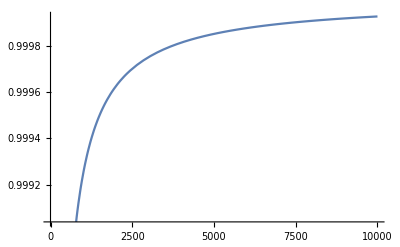

```mathematica
Plot[r[k,1],{k,1,10000}]
```

# Check the ricci for Lipkin

#### Test the Ric formula

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
Clear[gTest]
```

```mathematica
gTest[n_,λ_,χ_]={{-λ+3 χ^2, χ},
	{χ,λ^2-9}};
RicTestA[λ_,χ_]=ResourceFunction["RicciScalar"][gTest[n,λ,χ],{λ,χ}]//FullSimplify
```

(-9+56 χ^2+λ (-63+λ+5 λ^2-6 χ^2))/((28 χ^2+λ (-9+λ^2-3 λ χ^2))^2)

```mathematica
R1Test[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ,derTerms_?NumericQ,scale_?NumericQ]:=Module[{g,l,c,dg1,dg2,R12},
g=gTest[n,λ,χ];
dg1=ND[gTest[n,l,χ],l,λ];
dg2=ND[gTest[n,λ,c],c,χ];
1/(√(Abs@Det[g]))(g⟦1,2⟧/g⟦1,1⟧dg2⟦1,1⟧-dg1⟦2,2⟧)
]
R2Test[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ,derTerms_?NumericQ,scale_?NumericQ]:=Module[{g,l,c,dg1,dg2,R12},
g=gTest[n,λ,χ];
dg1=ND[gTest[n,l,χ],l,λ];
dg2=ND[gTest[n,λ,c],c,χ];
1/(√(Abs@Det[g]))(2dg1⟦1,2⟧-dg2⟦1,1⟧-g⟦1,2⟧/g⟦1,1⟧dg1⟦1,1⟧)
]
RicTest[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,derTermsIn,scale,g},
derTerms=5;
derTermsIn=5;
scale=0.01;
g=gTest[n,λ,χ];
1/(√(Abs@Det@g))(ND[R1Test[n,l,χ,derTermsIn,scale],l,λ]+ND[R2Test[n,λ,c,derTermsIn,scale],c,χ])
]
```

```mathematica
RicTest[2,-3.,-2.]
```

-21.4264

```mathematica
RicTestA[-3.,-2.]
```

21.875

```mathematica
gT={{-λ[]+3 χ[]^2, χ[]},
	{χ[],λ[]^2-9}};
```

```mathematica
(*Define the manifold*)
DefManifold[M1,2,{aaa,bbb}]
```

** DefManifold: Defining manifold M1.

** DefVBundle: Defining vbundle TangentM1.

```mathematica
(*Define coordinates on a chart of M*)
DefChart[ch1,M1,{0,1},{λ[],χ[]},ChartColor->Blue]
```

** DefChart: Defining chart ch1.

** DefTensor: Defining coordinate scalar λ[].

** DefTensor: Defining coordinate scalar χ[].

** DefMapping: Defining mapping ch1.

** DefMapping: Defining inverse mapping ich1.

** DefTensor: Defining mapping differential tensor dich1[-a,ich1aaa].

** DefTensor: Defining mapping differential tensor dch1[-aaa,ch1a].

** DefBasis: Defining basis ch1. Coordinated basis.

** DefCovD: Defining parallel derivative PDch1[-aaa].

** DefTensor: Defining vanishing torsion tensor TorsionPDch1[aaa,-bbb,-bbb1].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch1[aaa,-bbb,-bbb1].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch1[-aaa,-bbb,-bbb1,bbb2].

** DefTensor: Defining vanishing Ricci tensor RicciPDch1[-aaa,-bbb].

** DefTensor: Defining antisymmetric +1 density etaUpch1[aaa,bbb].

** DefTensor: Defining antisymmetric -1 density etaDownch1[-aaa,-bbb].

```mathematica
(*Create the metric tensor in terms of its coordinate components*)
met1=CTensor[gT,{-ch1,-ch1}]
```

CTensor[{{-λ+3 χ^2,χ},{χ,-9+λ^2}},{-ch1,-ch1},0]

```mathematica
(*Set this metric to be the metric of the manifold on the chart ch*)
SetCMetric[met1,ch1,SignatureOfMetric->{2,0,0}]
```

```mathematica
(*Define the covariant derivative operator*)
cd=CovDOfMetric[met1];
```

```mathematica
(*Calculate various curvature tensors and cache*)
MetricCompute[met1,ch1,All]
```

## Show the results

```mathematica
Riemann[cd][-a,-b,-c,-d]
```

0 | 0
0 | 0 | ● | ●
● | ●
● | ●
● | ● | 0 | 0
0 | 0 |   |   |   |  
a | b | c | d

```mathematica
Ricci[cd][-a,-b]
```

● | ●
● | ● |   |  
a | b

```mathematica
RicciScalar[cd][]
```

```mathematica
(-9+λ^2+5 λ^3+56 χ^2-3 λ (21+2 χ^2))/((-9 λ+λ^3+28 χ^2-3 λ^2 χ^2)^2)/.{λ[]->-3.,χ[]->-2}
```

21.875